## Eq.(126)-Eq.(127)toy models

### Eq.(126)

```mathematica
a[t_]:=Exp[t];k=1000;
```

```mathematica
DSolve[X''[t]+k^2/a[t]^2 X[t]==0,X[t],t]
```

{{X[t]→BesselJ[0,1000 √(ⅇ^(-2 t))] C[1]+2 BesselY[0,1000 √(ⅇ^(-2 t))] C[2]}}

```mathematica
a'[t]/a[t] a[t]
```

ⅇ^t

#### 需要满足k\gg aH

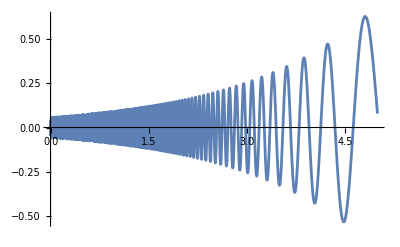

```mathematica
Plot[{BesselJ[0,1000 √(ⅇ^(-2 t))]+2 BesselY[0,1000 √(ⅇ^(-2 t))]},{t,0,5}]
```

### Eq.(127)

```mathematica
DSolve[X''[t]+3X'[t]==0,X[t],t]
```

{{X[t]→-1/3 ⅇ^(-3 t) C[1]+C[2]}}

#### 需要满足k\ll aH

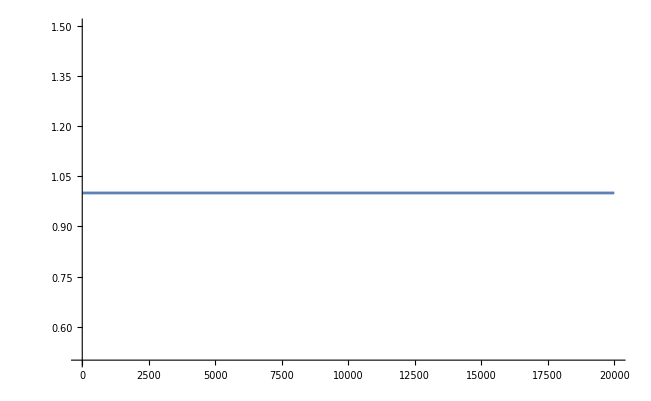

```mathematica
Plot[-1/3 ⅇ^(-3 t) +1,{t,10,20000},PlotRange->{{10,20000},{0.5,1.5}}]
```

### 数值求解

```mathematica
DSolve[X''[t]+3X'[t]+k^2/a[t]^2 X[t]==0,X[t],t]
```

{{X[t]→ⅇ^(1000 ⅈ √(ⅇ^(-2 t))) (ⅈ+1000 √(ⅇ^(-2 t))) C[1]+(ⅇ^(-1000 ⅈ √(ⅇ^(-2 t))) (1+1000 ⅈ √(ⅇ^(-2 t))) C[2])/1000000000}}

#### 此处未考虑初始条件（BD真空）

```mathematica
f[t_]:=Re[ⅇ^(1000 ⅈ √(ⅇ^(-2 t))) (ⅈ+1000 √(ⅇ^(-2 t))) +(ⅇ^(-1000 ⅈ √(ⅇ^(-2 t))) (1+1000 ⅈ √(ⅇ^(-2 t))))/1000000000]
```

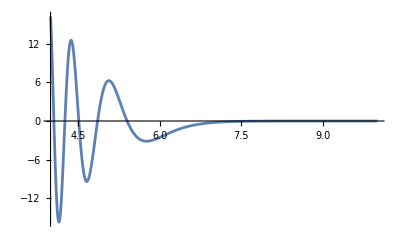

```mathematica
Plot[f[t],{t,4,10},PlotRange->All]
```